```mathematica
$Assumptions=
   N>1&&Element[N,Integers]&&
lambda>0&&
lambdaBar>0&&
delta>0&&
NlambdaBar>0&&
Delta0>0&&
alpha>1;
```

```mathematica
(*1   ExponentialDistribution*)
(*1.1 Define parameters*)
lambdaBarExp[N_]:=1/(600*N);
expr[N_,delta_]:=1-(1+delta*lambdaBarExp[N])^(1-N);
```

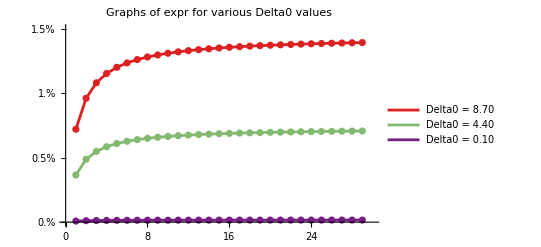

```mathematica
(*1.2 Plot fork rate*)
deltaValues=Reverse[Subdivide[0.1,8.7,2]];
plots=Table[ListPlot[Table[expr[N,delta],{N,2,30}],Mesh->All,Joined->True,PlotRange->{{0,30},{0,0.015}},PlotStyle->ColorData["Rainbow"][(delta-0.1)/(8.7-0.1)],PlotLegends->{"Delta0 = "<>ToString[NumberForm[delta,{Infinity,2}]]}],{delta,deltaValues}];
percentTicks=Table[{i,ToString[100 i]<>"%"},{i,0,0.015,0.005}];
Show[plots,PlotLabel->"Graphs of expr for various Delta0 values",Ticks->{Automatic,percentTicks}]
```

```mathematica
lambdaBarExp[N_]:=1/(600*N);
expr[N_,delta_]:=1-(1+delta*lambdaBarExp[N])^(1-N);
Print[expr[19,10000]];
```

3379891934663564100822593527382633800/3379932275732534791891466777752413049

```mathematica
(*1.3 export*)combinedDataExp=Table[Flatten[{N,Table[expr[N,delta],{delta,deltaValues}]}],{N,2,30}];

Export["combined_data_exp.csv",combinedDataExp,"TableHeadings"->{"N","Delta1","Delta2","Delta3"}]

(*SystemOpen["combined_data_exp.csv"]*)
```

combined_data_exp.csv

```mathematica
(*1.4 specific data*)
deltaValuesProp={7.12, 8.7, 0.86};
expr[19,deltaValuesProp]
```

{0.0111757,0.0136378,0.00135692}

```mathematica
deltaValuesProp={1, 10, 100, 1000,10000};
Print[N[expr[19,deltaValuesProp]]];
```

{16710091371979169064310878522694340956627794661453385735094175788085201/10591879275624818727773655813934144196956627794661453385735094175788085201,168227198447291918369456900207300585703910642895563321/10743396382700131477078801835618750441703910642895563321,1800284420999419830406442570692065769/12375453605252259389115787506103515625,142911643190338593709561873877455/183252712161029662582812243656704,3379891934663564100822593527382633800/3379932275732534791891466777752413049}

```mathematica
(*1.5 change n(change shape)*)
```

```mathematica
lambdaBarExp[N_]=1/(600*N);
expr[N_,delta_]=1-(1+delta*lambdaBarExp[N])^(1-N);
delta=8.7; 
results=Table[expr[N,delta],{N,2,22}];
Export["cdeltaResultN_exp.csv",results]
```

cdeltaResultN_exp.csv

```mathematica
(*1.6 change Delta0*)
lambdaBarExp[N_]:=1/(600*N);
expr[N_,delta_]:=1-(1+delta*lambdaBarExp[N])^(1-N);
n=19; 
results=Table[N[expr[n,delta]],{delta,1,10000,500}];
Export["cdeltaResultN_exp_Delta0.csv",results]
```

cdeltaResultN_exp_Delta0.csv

```mathematica
SystemOpen["cdeltaResultN_exp_Delta0.csv"]
```

```mathematica
SystemOpen["cdeltaResultN_exp_Delta0.csv"]
```

```mathematica
(*2  log-normal*)
(*2.1 define cdelta*)
dist[lambdaBar_,sigma_]:=LogNormalDistribution[Log[lambdaBar]-sigma^2/2,sigma];(*Sqrt[2*log[lambdaBar]]*)
B2N[lambdaBar_?NumericQ,delta_?NumericQ,sigma_?NumericQ]:=NIntegrate[lambda*Exp[-lambda*delta]*PDF[dist[lambdaBar,sigma],lambda],{lambda,0.0000001,∞}];
C2N[lambdaBar_?NumericQ,delta_?NumericQ,sigma_?NumericQ]:=NIntegrate[Exp[-lambda*delta]*PDF[dist[lambdaBar,sigma],lambda],{lambda,0.0000001,∞}];
cdeltaResultN[lambdaBar_,n_,Delta0_,sigma_]:=NIntegrate[(n-1)*B2N[lambdaBar,delta,sigma]*C2N[lambdaBar,delta,sigma]^(n-2),{delta,0,Delta0}];
```

Table::iterb: Iterator {delta,deltaValues} does not have appropriate bounds.

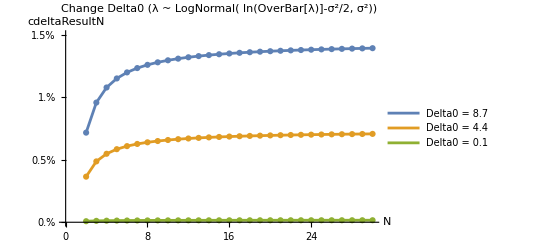

```mathematica
(*2.2 plot*)
sigma=1.11491086615159;

plotData=Table[Table[cdeltaResultN[1/(600*n),n,delta,sigma],{n,2,30}],{delta,deltaValues}];

deltaValues=Reverse[Subdivide[0.1,8.7,2]];
ListPlot[plotData,Mesh->All,Joined->True,PlotRange->{{0,30},{0,0.015}},DataRange->{2,30},AxesLabel->{"N","cdeltaResultN"},Ticks->{Automatic,Table[{i,ToString[100 i]<>"%"},{i,0,0.015,0.005}]},PlotLegends->Table["Delta0 = "<>ToString[delta],{delta,deltaValues}],PlotLabel->Style["Change Delta0 (λ ~ LogNormal( ln(OverBar[λ)]-σ^2/2, σ^2))",Bold]]
```

```mathematica
(*2.3 export*)
exportData=Transpose[Join[{Range[2,30]},Transpose[plotData]]];
Export["combined_data_logn.csv",exportData,"TableHeadings"->Prepend["N"<>ToString[NumberForm[#,{Infinity,2}]]&/@deltaValues,"N"]]
```

Transpose::nmtx: The first two levels of {{2,3,4,5,6,7,8,9,10,11,«19»},{0.00716138,0.0036437,0.0000833213},{0.00956421,0.00486245,0.000111097},«5»,{0.0127811,0.00649084,0.000148134},{0.0129423,0.00657236,0.000149986},«20»} cannot be transposed.

combined_data_logn.csv

```mathematica
SystemOpen["combined_data_logn.csv"]
```

```mathematica
(*2.4 specific values*)
sigma=1.11491086615159;
deltaValuesProp={7.12, 8.7, 0.86};
cdeltaResultN[1/11400,19,deltaValuesProp,sigma];
```

NIntegrate::nlim: delta = {7.12,8.7,0.86} is not a valid limit of integration.

```mathematica
cdeltaResultN[1/11400,19,7.12,1.11491086615159];
```

```mathematica
0.01117060866114965
```

0.0111706

```mathematica
cdeltaResultN[1/11400,19,8.7,1.11491086615159];
```

```mathematica
0.013630211472182518
```

0.0136302

```mathematica
cdeltaResultN[1/11400,19,0.86,1.11491086615159];
```

```mathematica
0.0013568467297459667
```

0.00135685

```mathematica
(*2.5 change sigma*)
n=19;
Delta0=8.7;

results=Table[{sigma,cdeltaResultN[1/(n*600),n,Delta0,sigma]},{sigma,0.5,2.5,0.1}];
Export["cdeltaResultN_logn.csv",results]
```

cdeltaResultN_logn.csv

```mathematica
(*2.6 change delta0*)
n=19;
sigma=1.11491086615159;
results=Table[{Delta0,cdeltaResultN[1/(n*600),n,Delta0,sigma]},{Delta0,0.1,9.1,0.5}];
Export["cdeltaResultN_logn_Delta0.csv",results]
```

cdeltaResultN_logn_Delta0.csv

```mathematica
SystemOpen["cdeltaResultN_logn_Delta0.csv"]
```

```mathematica
cdeltaResultN[1/11400,19,10000,1.11491086615159];
```

```mathematica
0.9999588238156539
```

0.999959

```mathematica
(*2.7 find root*)
n=9;
Delta0=8.7;
Print[100*cdeltaResultN[1/(600*n),n,Delta0,2.88]];
```

0.415258

```mathematica
results={};

For[n=2,n<=30,n++,Delta0=8.7;
target=0.41;
minDifference=Infinity;
bestSigma=0;
Do[result=100*cdeltaResultN[1/(600*n),n,Delta0,sigma];
difference=Abs[result-target];
If[difference<minDifference,minDifference=difference;
bestSigma=sigma;,
Break[]; ],{sigma,2,3.1,0.01}];AppendTo[results,{n,bestSigma,minDifference}];]

Export["results_logn.csv",results,"CSV"]
```

results_logn.csv

```mathematica
SystemOpen["results_logn.csv"]
```

```mathematica
SystemOpen["results_logn.csv"]
```

```mathematica
(*2.8 data near isoline*)
SetDirectory["/Users/yuyao/Documents/research/forks/Mathematica nb"];
Directory[]
```

/Users/yuyao/Documents/research/forks/Mathematica nb

```mathematica
Delta0=8.7;
data=Import["results_iso_logn.csv","CSV","HeaderLines"->1];

processedData=Table[With[{n=row[[1]],sigma=row[[4]]},lambdaBar=1/(600*n);
{n,sigma,cdeltaResultN[lambdaBar,n,Delta0,sigma]}],{row,data}];

(*Save the updated data to a new CSV file*)
Export["results_iso_logn_forkrate.csv",Join[{{"n","Sigma","cdeltaResultN"}},processedData],"CSV"];
```

```mathematica
8.7
```

8.7

```mathematica
(*Lomax*)
```

```mathematica
(*3.1 define cdelta*)
dist[lambdaBar_,alpha_]:=ParetoDistribution[lambdaBar(alpha-1),alpha,0];
B3N[lambdaBar_,delta_,alpha_]:=Integrate[lambda*Exp[-lambda*delta]*PDF[dist[lambdaBar,alpha],lambda],{lambda,0,∞}];
C3N[lambdaBar_,delta_,alpha_]:=Integrate[Exp[-lambda*delta]*PDF[dist[lambdaBar,alpha],lambda],{lambda,0,∞}];
pdeltaN[lambdaBar_,N_,delta_,alpha_]:=(N-1)*B3N[lambdaBar,delta,alpha]*C3N[lambdaBar,delta,alpha]^(N-2);
pdeltaResultN=pdeltaN[lambdaBar,N,delta,alpha];
cdeltaResultN[lambdaBar_,n_,Delta0_,alpha_]:=NIntegrate[pdeltaN[lambdaBar,n,delta,alpha],{delta,0,Delta0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in delta near {delta} = {0.000156489}. NIntegrate obtained 0.0126379 and 1.47325×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in delta near {delta} = {0.000491902}. NIntegrate obtained 0.0126654 and 2.98223×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in delta near {delta} = {0.0000791436}. NIntegrate obtained 0.00651641 and 7.96469×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

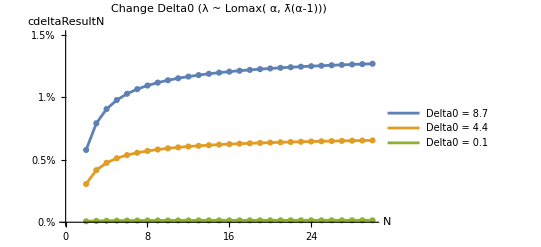

```mathematica
(*3.2 Plot*)
alpha=1.30092456355467;
deltaValues=Reverse[Subdivide[0.1,8.7,2]];
plotData=Table[Table[cdeltaResultN[1/(600*n),n,delta,alpha],{n,2,30}],{delta,deltaValues}];

ListPlot[plotData,Mesh->All,Joined->True,PlotRange->{{0,30},{0,0.015}},DataRange->{2,30},AxesLabel->{"N","cdeltaResultN"},Ticks->{Automatic,Table[{i,ToString[100 i]<>"%"},{i,0,0.015,0.005}]},PlotLegends->Table["Delta0 = "<>ToString[delta],{delta,deltaValues}],PlotLabel->Style["Change Delta0 (λ ~ Lomax( α, λ̄(α-1)))",Bold]]
```

```mathematica
(*3.3 export*)
exportData=Transpose[Join[{Range[2,30]},Transpose[plotData]]];
Export["combined_data_lomax.csv",exportData,"TableHeadings"->Prepend["N"<>ToString[NumberForm[#,{Infinity,2}]]&/@deltaValues,"N"]]
```

Transpose::nmtx: The first two levels of {{2,3,4,5,6,7,8,9,10,11,«19»},{0.00577901,0.00305782,0.000078868},{0.0079096,0.00416457,0.000105838},«5»,{0.0111571,0.00581166,0.000143089},{0.0113469,0.00590549,0.000145036},«20»} cannot be transposed.

combined_data_lomax.csv

```mathematica
(*3.4 specific data*)
alpha=1.30092456355467;
deltaValuesProp={7.12, 8.7, 0.86};
cdeltaResultN[1/(600*19),19,deltaValuesProp,alpha]
```

NIntegrate::nlim: delta = {7.12,8.7,0.86} is not a valid limit of integration.

NIntegrate[pdeltaN[1/11400,19,delta,1.30092],{delta,0,{7.12,8.7,0.86}}]

```mathematica
cdeltaResultN[1/11400,19,7.12,1.30092456355467];
```

```mathematica
0.01009142745114652
```

0.0100914

```mathematica
cdeltaResultN[1/11400,19,0.86,1.30092456355467];
```

```mathematica
0.0012864953662894076
```

0.0012865

```mathematica
cdeltaResultN[1/11400,19,8.7,1.30092456355467];
```

```mathematica
0.012235505566459966
```

0.0122355

```mathematica
(*3.5 change alpha*)
n=19;
Delta0=8.7;

results=Table[{alpha,cdeltaResultN[1/(n*600),n,Delta0,alpha]},{alpha,1.1,3.1,0.1}];
Export["cdeltaResultN_lomax.csv",results]
```

cdeltaResultN_lomax.csv

```mathematica
(*3.6 change Delta0*)
n=19;
alpha=1.30092456355467;

results=Table[{Delta0,cdeltaResultN[1/(n*600),n,Delta0,alpha]},{Delta0,0.1,9.1,0.5}];
Export["cdeltaResultN_lomax_Delta0.csv",results]
```

cdeltaResultN_lomax_Delta0.csv

```mathematica
SystemOpen["cdeltaResultN_lomax_Delta0.csv"]
```

```mathematica
cdeltaResultN[1/11400,19,1000,1.30092456355467];
```

```mathematica
0.6166834797058254
```

0.616683

```mathematica
cdeltaResultN[1/11400,19,2000,1.30092456355467];
```

```mathematica
0.816607794598492
```

0.816608

```mathematica
cdeltaResultN[1/11400,19,10000,1.30092456355467];
```

```mathematica
0.9966307116884683
```

0.996631

```mathematica
(*3.7 find root*)
n=30;
Delta0=8.7;
Print[100*cdeltaResultN[1/(600*n),n,Delta0,1.03]];
```

0.416996

```mathematica
results={};

For[n=13,n<=30,n++,Delta0=8.7;
target=0.41;
minDifference=Infinity;
bestAlpha=0;
Do[result=100*cdeltaResultN[1/(600*n),n,Delta0,alpha];
difference=Abs[result-target];
If[difference<minDifference,minDifference=difference;
bestAlpha=alpha,Break[]; ],{alpha,1.033,1.04,0.001}];AppendTo[results,{n,bestAlpha,minDifference}];]

Export["results_lomax.csv",results,"CSV"]
```

results_lomax.csv

```mathematica
SystemOpen["results_lomax.csv"]
```

```mathematica
(*3.8 data near iso*)
SetDirectory["/Users/yuyao/Documents/research/forks/Mathematica nb"];
Directory[]
```

/Users/yuyao/Documents/research/forks/Mathematica nb

```mathematica
Delta0=8.7;
data=Import["results_iso_lomax.csv","CSV","HeaderLines"->1];
numRows=Length[data];

processedData=Table[0,{numRows},{3}]; (*Initialize an empty array*)

For[i=1,i<=numRows,i++,row=data[[i]];
With[{n=row[[1]],alpha=row[[4]]},lambdaBar=1/(600*n);
(*Calculate and store the result*)processedData[[i]]={n,alpha,cdeltaResultN[lambdaBar,n,Delta0,alpha]};
(*Display progress as percentage*)Print["Processing: ",N[100*i/numRows],"%"];];];

(*Save the updated data to a new CSV file*)
Export["results_iso_lomax_forkrate.csv",Join[{{"n","Alpha","cdeltaResultN"}},processedData],"CSV"];
```

Processing: 0.574713%

Processing: 1.14943%

Processing: 1.72414%

Processing: 2.29885%

Processing: 2.87356%

Processing: 3.44828%

Processing: 4.02299%

Processing: 4.5977%

Processing: 5.17241%

Processing: 5.74713%

Processing: 6.32184%

Processing: 6.89655%

Processing: 7.47126%

Processing: 8.04598%

Processing: 8.62069%

Processing: 9.1954%

Processing: 9.77011%

Processing: 10.3448%

Processing: 10.9195%

Processing: 11.4943%

Processing: 12.069%

Processing: 12.6437%

Processing: 13.2184%

Processing: 13.7931%

Processing: 14.3678%

Processing: 14.9425%

Processing: 15.5172%

Processing: 16.092%

Processing: 16.6667%

Processing: 17.2414%

Processing: 17.8161%

Processing: 18.3908%

Processing: 18.9655%

Processing: 19.5402%

Processing: 20.1149%

Processing: 20.6897%

Processing: 21.2644%

Processing: 21.8391%

Processing: 22.4138%

Processing: 22.9885%

Processing: 23.5632%

Processing: 24.1379%

Processing: 24.7126%

Processing: 25.2874%

Processing: 25.8621%

Processing: 26.4368%

Processing: 27.0115%

Processing: 27.5862%

Processing: 28.1609%

Processing: 28.7356%

Processing: 29.3103%

Processing: 29.8851%

Processing: 30.4598%

Processing: 31.0345%

Processing: 31.6092%

Processing: 32.1839%

Processing: 32.7586%

Processing: 33.3333%

Processing: 33.908%

Processing: 34.4828%

Processing: 35.0575%

Processing: 35.6322%

Processing: 36.2069%

Processing: 36.7816%

Processing: 37.3563%

Processing: 37.931%

Processing: 38.5057%

Processing: 39.0805%

Processing: 39.6552%

Processing: 40.2299%

Processing: 40.8046%

Processing: 41.3793%

Processing: 41.954%

Processing: 42.5287%

Processing: 43.1034%

Processing: 43.6782%

Processing: 44.2529%

Processing: 44.8276%

Processing: 45.4023%

Processing: 45.977%

Processing: 46.5517%

Processing: 47.1264%

Processing: 47.7011%

Processing: 48.2759%

Processing: 48.8506%

Processing: 49.4253%

Processing: 50.%

Processing: 50.5747%

Processing: 51.1494%

Processing: 51.7241%

Processing: 52.2989%

Processing: 52.8736%

Processing: 53.4483%

Processing: 54.023%

Processing: 54.5977%

Processing: 55.1724%

Processing: 55.7471%

Processing: 56.3218%

Processing: 56.8966%

Processing: 57.4713%

Processing: 58.046%

Processing: 58.6207%

Processing: 59.1954%

Processing: 59.7701%

Processing: 60.3448%

Processing: 60.9195%

Processing: 61.4943%

Processing: 62.069%

Processing: 62.6437%

Processing: 63.2184%

Processing: 63.7931%

Processing: 64.3678%

Processing: 64.9425%

Processing: 65.5172%

Processing: 66.092%

Processing: 66.6667%

Processing: 67.2414%

Processing: 67.8161%

Processing: 68.3908%

Processing: 68.9655%

Processing: 69.5402%

Processing: 70.1149%

Processing: 70.6897%

Processing: 71.2644%

Processing: 71.8391%

Processing: 72.4138%

Processing: 72.9885%

Processing: 73.5632%

Processing: 74.1379%

Processing: 74.7126%

Processing: 75.2874%

Processing: 75.8621%

Processing: 76.4368%

Processing: 77.0115%

Processing: 77.5862%

Processing: 78.1609%

Processing: 78.7356%

Processing: 79.3103%

Processing: 79.8851%

Processing: 80.4598%

Processing: 81.0345%

Processing: 81.6092%

Processing: 82.1839%

Processing: 82.7586%

Processing: 83.3333%

Processing: 83.908%

Processing: 84.4828%

Processing: 85.0575%

Processing: 85.6322%

Processing: 86.2069%

Processing: 86.7816%

Processing: 87.3563%

Processing: 87.931%

Processing: 88.5057%

Processing: 89.0805%

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in delta near {delta} = {0.0970251}. NIntegrate obtained 0.013696 and 5.05963×10^-7 for the integral and error estimates.

Processing: 89.6552%

Processing: 90.2299%

Processing: 90.8046%

Processing: 91.3793%

Processing: 91.954%

Processing: 92.5287%

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in delta near {delta} = {0.154919}. NIntegrate obtained 0.0136235 and 5.20293×10^-7 for the integral and error estimates.

Processing: 93.1034%

Processing: 93.6782%

Processing: 94.2529%

Processing: 94.8276%

Processing: 95.4023%

Processing: 95.977%

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in delta near {delta} = {0.234325}. NIntegrate obtained 0.0135125 and 5.97952×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Processing: 96.5517%

Processing: 97.1264%

Processing: 97.7011%

Processing: 98.2759%

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Processing: 98.8506%

Processing: 99.4253%

Processing: 100.%